0

1000000

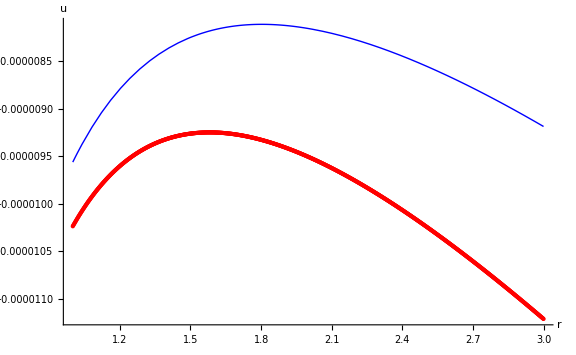

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
numSolution=ReadList["axis.txt", {Number, Number}];
settings = ReadList["axisSettings.txt",Number];
h =settings[[1]];a =settings[[2]];b =settings[[3]];
Pa =settings[[4]]
Pb=settings[[5]]
e=settings[[6]];
nu=settings[[7]];
mu =e/(2(1+nu));
lambda = (nu * e)/((1+nu)(1-2 nu));
exactSol[r_]= (1-2nu)/e*(Pa  a^2-Pb  b^2)/(b^2-a^2)r+(1 + nu)/e * (a^2 b^2)/r * (Pa -Pb)/(b^2-a^2)(*Феодосьев*);
u1=exactSol[0.04];
exactSol[0.03];
plot = ListPlot[numSolution , PlotStyle->{Red,Tiny[Large]},PlotTheme->"Classic",AxesLabel->{r,u}, ImageSize->Large];
plot1 =Plot[exactSol[r],{r, a,b},PlotTheme->"Classic",AxesLabel->{r,u},PlotStyle->{Thick, Blue},ImageSize->Large];
Show[plot, plot1,PlotRange->Full]
realIntegrate[f_,x_Symbol]:=Simplify[Integrate[f,x]/. Log[expr_]:>Log[Abs[expr]],x∈Reals];
(*Export["ff.pdf",k]*)
```

```mathematica
(*Считаем коэффициенты*)
(*Subscript[a, i]*)
```

```mathematica
a= r1i;
b = ri;
Fi[x_]:=(x-r1i)/(ri-r1i);
F1i[x_]:=(x-ri)/(r1i-ri);
inta = realIntegrate[Fi[x] F1i[x]/x,x]/.x->a;
intb=realIntegrate[Fi[x] F1i[x]/x,x]/.x->b;
ai = (lambda + 2 mu)*(D[Fi[x],x] D[F1i[x],x] Integrate[x,{x,a,b}] +intb-inta) + 
lambda*(D[Fi[x],x] Integrate[F1i[x],{x,a,b}]+D[F1i[x],x] Integrate[Fi[x],{x,a,b}])/.{r1i->0.03, ri->0.04}
```

-9.29434×10^8

```mathematica
(*Subscript[c, i]*)
a= ri;
b = ri1;
Fi[x_]:=(x-ri1)/(ri-ri1);
Fi1[x_]:=(x-ri)/(ri1-ri);
inta = realIntegrate[Fi[x] Fi1[x]/x,x]/.x->a;
intb=realIntegrate[Fi[x] Fi1[x]/x,x]/.x->b;
ci = (lambda + 2 mu)*(D[Fi[x],x] D[Fi1[x],x] Integrate[x,{x,a,b}] +intb-inta) + 
lambda*(D[Fi[x],x] Integrate[Fi1[x],{x,a,b}]+D[Fi1[x],x] Integrate[Fi[x],{x,a,b}])/.{ri->0.03, ri1->0.04}
```

-9.29434×10^8

```mathematica
(*bi_1*)
a=ri;
b=ri1;
Fi[x_]:=(x-ri1)/(ri-ri1);
inta = realIntegrate[Fi[x] Fi[x]/x,x]/.x->a;
intb=realIntegrate[Fi[x] Fi[x]/x,x]/.x->b;
bi1=(lambda + 2 mu)*(D[Fi[x],x] D[Fi[x],x] Integrate[x,{x,a,b}] +intb-inta) + 
2 lambda D[Fi[x],x] Integrate[Fi[x],{x,a,b}]/.{ri->0.03, ri1->0.04}
```

8.5463×10^8

```mathematica
(*bi_2*)
a=r1i;
b=ri;
Fi[x_]:=(x-r1i)/(ri-r1i);
inta = realIntegrate[Fi[x] Fi[x]/x,x]/.x->a;
intb=realIntegrate[Fi[x] Fi[x]/x,x]/.x->b;
bi2=(lambda + 2 mu)*(D[Fi[x],x] D[Fi[x],x] Integrate[x,{x,a,b}] +intb-inta) + 
2 lambda D[Fi[x],x] Integrate[Fi[x],{x,a,b}]/.{r1i->0.03, ri->0.04}
```

1.08169×10^9

```mathematica
(*bi*)
bi=bi1+bi2
```

1.93632×10^9

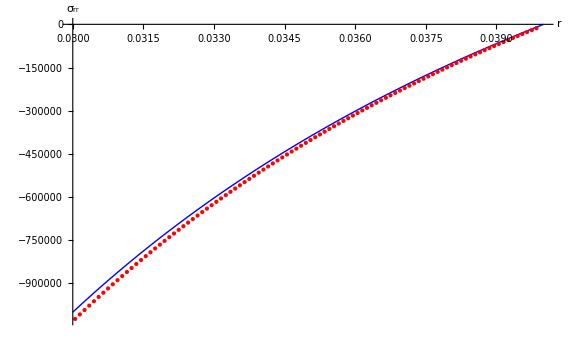

```mathematica
sigmaRR={};
error=0;
exactSigmaRR[r_]= (Pa  a^2-Pb  b^2)/(b^2-a^2)- (a^2 b^2)/r^2 * (Pa -Pb)/(b^2-a^2);

sigmaRR=ReadList["sigmaRR.txt", {Number, Number}];
p1=numSigmaRRPlot=ListPlot[sigmaRR, PlotStyle->{Red,Tiny[Large]},PlotTheme->"Classic",AxesLabel->{r,Subscript[σ, rr]}, ImageSize->Large];
exactSigmaRR[a];
p2=exactSigmaRRPlot=Plot[exactSigmaRR[r],{r, a,b},PlotTheme->"Classic",AxesLabel->{r,Subscript[σ, rr]},PlotStyle->{Thick, Blue},ImageSize->Large, PlotRange->All];
Show[p2,p1]
```

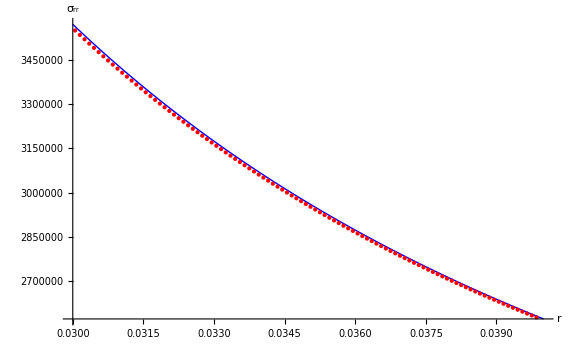

```mathematica
sigmaFF={};
error=0;
exactSigmaFF[r_]= (Pa  a^2-Pb  b^2)/(b^2-a^2)+ (a^2 b^2)/r^2 * (Pa -Pb)/(b^2-a^2);
sigmaFF=ReadList["sigmaFF.txt", {Number, Number}];
numSigmaFFPlot=ListPlot[sigmaFF, PlotStyle->{Red,Tiny[Large]},PlotTheme->"Classic",AxesLabel->{r,Subscript[σ, ϕϕ]}, ImageSize->Large];
exactSigmaFFPlot=Plot[exactSigmaFF[r],{r, a,b},PlotTheme->"Classic",AxesLabel->{r,Subscript[σ, rr]},PlotStyle->{Thick, Blue},ImageSize->Large, PlotRange->All];
Show[exactSigmaFFPlot,numSigmaFFPlot]
```

```mathematica
ClearAll["Global`*"];
CForm[ (1-2nu)/e*(Pa  a^2-Pb  b^2)/(b^2-a^2)r+(1 + nu)/e * (a^2 b^2)/r * (Pa -Pb)/(b^2-a^2)]
```

(Power(a,2)*Power(b,2)*(1 + nu)*(Pa - Pb))/((-Power(a,2) + Power(b,2))*e*r) + 
   ((1 - 2*nu)*(Power(a,2)*Pa - Power(b,2)*Pb)*r)/((-Power(a,2) + Power(b,2))*e)